El camino mas corto desde Esmeraldas a Nueva Loja es: {5,23,17,13} y la distancia del camino tomado es: 547.km, tal como se muestra en el grafo a continuacion:

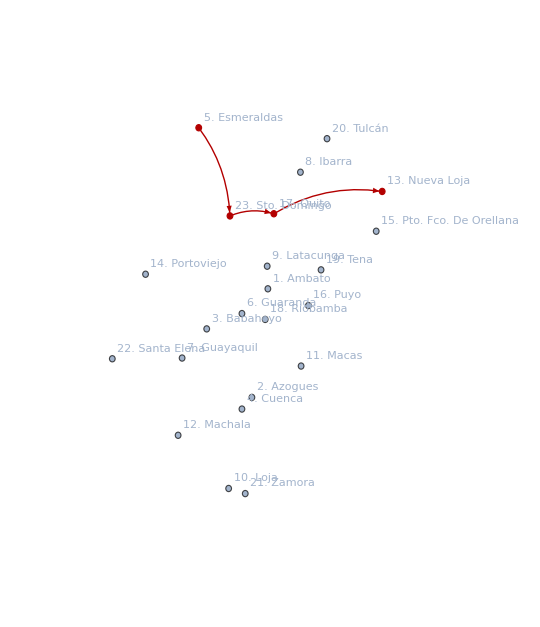
-Graphics--Graphics-

El camino mas corto desde Esmeraldas a Santa Elena es: {5,14,22} y la distancia que existe entre las 2 ciudades es: 41km, tal como se muestra en el grafo a continuacion:

El camino mas corto desde Tulcán a Macas es: {20,11} y la distancia que existe entre las 2 ciudades es: 616.km, tal como se muestra en el grafo a continuacion:

El camino mas corto desde Tulcán a Loja es: {20,10} y la distancia que existe entre las 2 ciudades es: 909.km, tal como se muestra en el grafo a continuacion:

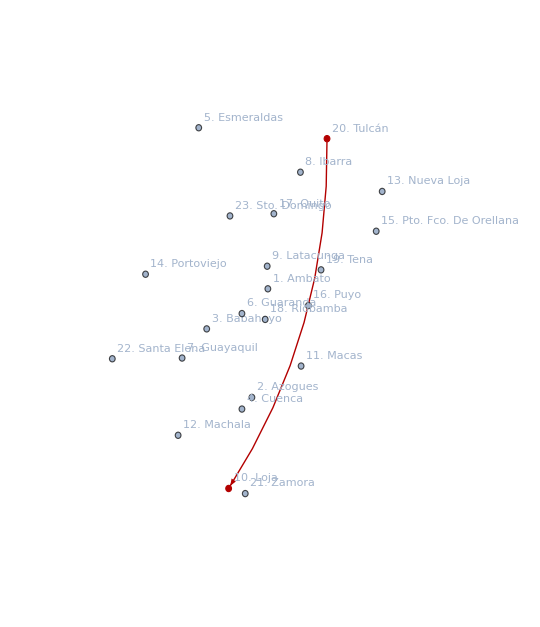
-Graphics--Graphics-

```mathematica
CoordNodos={{-78.61,-1.25},{-78.85,-2.74},{-79.53,-1.80},{-79.00,-2.90},{-79.65,0.96},{-79.00,-1.59},{-79.90,-2.20},{-78.12,0.35},{-78.62,-0.94},{-79.20,-3.99},{-78.11,-2.31},{-79.96,-3.26},{-76.89,0.086},{-80.45,-1.05},{-76.98,-0.46},{-78.00,-1.48},{-78.52,-0.22},{-78.65,-1.67},{-77.81,-0.99},{-77.72,0.81},{-78.95,-4.06},{-80.95,-2.21},{-79.18,-0.25}};
Nodos=Table[i,{i,1,Length[CoordNodos]}];
NodosCiudades = {"1. Ambato","2. Azogues","3. Babahoyo","4. Cuenca","5. Esmeraldas","6. Guaranda","7. Guayaquil","8. Ibarra","9. Latacunga","10. Loja","11. Macas","12. Machala","13. Nueva Loja","14. Portoviejo","15. Pto. Fco. De Orellana","16. Puyo","17. Quito","18. Riobamba","19. Tena","20. Tulcán","21. Zamora","22. Santa Elena","23. Sto. Domingo"};
Ciudades = {"Ambato","Azogues","Babahoyo","Cuenca","Esmeraldas","Guaranda","Guayaquil","Ibarra","Latacunga","Loja","Macas","Machala","Nueva Loja","Portoviejo","Pto. Fco. De Orellana","Puyo","Quito","Riobamba","Tena","Tulcán","Zamora","Santa Elena","Sto. Domingo"};
Distancias = Import["C:\\Users\\Kempis\\Desktop\\Proyecto Discretas\\Ecuador_Distancias.xlsx",{"Data",1,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23}}];
Etq = Table[i->NodosCiudades[[i]],{i,1,Length[CoordNodos]}];
img =Import["C:\\Users\\Kempis\\Desktop\\Proyecto Discretas\\Ecuador.png"];

Aristas=List[];
Peso=List[];
For[i=1,i≤Length[Distancias],i++,
For[j=1,j≤Length[Distancias],j++,
AppendTo[Aristas,i-> j];]

];

For[i=1,i≤Length[Distancias],i++,
For[j=1,j≤Length[Distancias],j++,
AppendTo[Peso,Distancias[[i]][[j]]];
];
];
G=Graph[Nodos,Aristas,VertexCoordinates->CoordNodos,VertexLabels->Etq,EdgeWeight->Peso,EdgeStyle->Opacity[0], ImageSize->540];

aux =0;
While[aux==0,
Inicio = Input["Inserte en la ciudad que se encuentra:"];
Destino =Input["Inserte su destino:"];
If[(Inicio<1||Inicio>23)||(Destino<1||Destino>23),aux=0,aux=1];
];

sp= FindShortestPath[G,Inicio, Destino];
sum=0;
For[i=1,i≤Length[sp]-1,i++,
j=i+1;
sum+=Distancias[[sp[[i]]]][[sp[[j]]]];
];

Print["El camino mas corto desde ",Ciudades[[Inicio]]," a ",Ciudades[[Destino]]," es: ",sp," y la distancia del camino tomado es: ",sum,"km, tal como se muestra en el grafo a continuacion: "]
Overlay[{img,HighlightGraph[G,PathGraph[sp,DirectedEdges->True]]}]
```

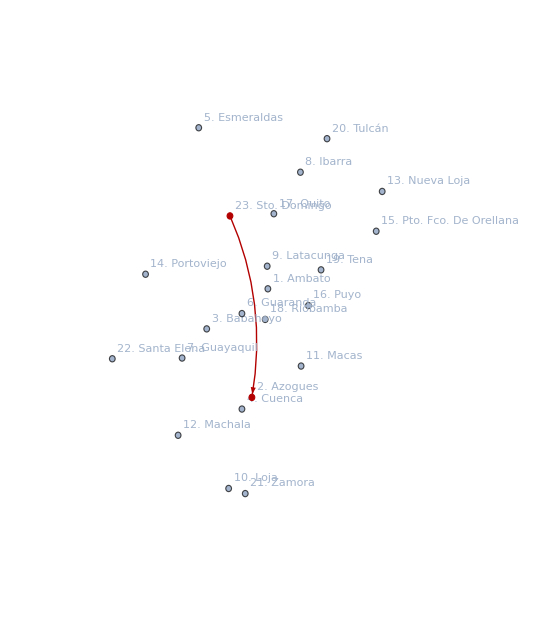
```mathematica
-Graphics--Graphics-
```

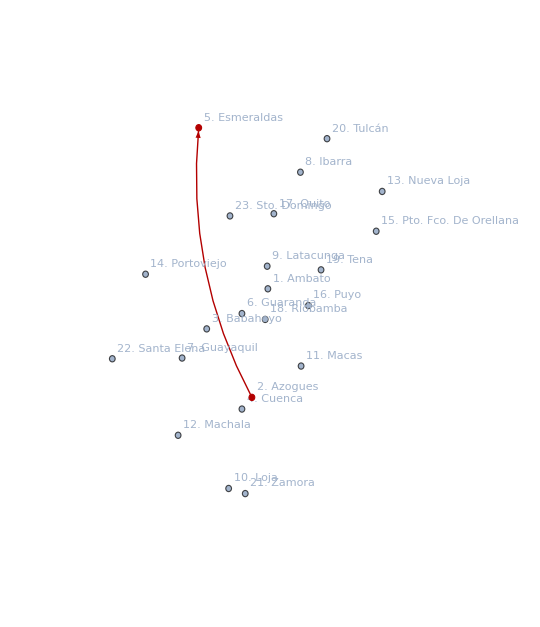
```mathematica
-Graphics--Graphics-
```